Plot the Barbosa [1977] formula for a few different potentials/thermal temperatures

```mathematica
barb[α_,vOvera_]:=1+(2(1-α)vOvera Exp[-α vOvera^2])/Erfc[-vOvera] NIntegrate[Exp[α x^2]Erfc[x],{x,-vOvera,∞}]
```

```mathematica
barbAlt[oneOver_,vOvera_]:=1+(2(1-oneOver)vOvera Exp[-oneOver vOvera^2])/Erfc[-vOvera] NIntegrate[Exp[oneOver x^2]Erfc[x],{x,-vOvera,∞}]
```

```mathematica
alphaList=Range[0.005,0.995,0.005];
```

```mathematica
alphaList=PowerRange[0.000001,0.9999,1.1]
```

{1.×10^-6,1.1×10^-6,1.21×10^-6,1.331×10^-6,1.4641×10^-6,1.61051×10^-6,1.77156×10^-6,1.94872×10^-6,2.14359×10^-6,2.35795×10^-6,2.59374×10^-6,2.85312×10^-6,3.13843×10^-6,3.45227×10^-6,3.7975×10^-6,4.17725×10^-6,4.59497×10^-6,5.05447×10^-6,5.55992×10^-6,6.11591×10^-6,6.7275×10^-6,7.40025×10^-6,8.14027×10^-6,8.9543×10^-6,9.84973×10^-6,0.0000108347,0.0000119182,0.00001311,0.000014421,0.0000158631,0.0000174494,0.0000191943,0.0000211138,0.0000232252,0.0000255477,0.0000281024,0.0000309127,0.0000340039,0.0000374043,0.0000411448,0.0000452593,0.0000497852,0.0000547637,0.0000602401,0.0000662641,0.0000728905,0.0000801795,0.0000881975,0.0000970172,0.000106719,0.000117391,0.00012913,0.000142043,0.000156247,0.000171872,0.000189059,0.000207965,0.000228762,0.000251638,0.000276801,0.000304482,0.00033493,0.000368423,0.000405265,0.000445792,0.000490371,0.000539408,0.000593349,0.000652683,0.000717952,0.000789747,0.000868722,0.000955594,0.00105115,0.00115627,0.0012719,0.00139908,0.00153899,0.00169289,0.00186218,0.0020484,0.00225324,0.00247856,0.00272642,0.00299906,0.00329897,0.00362887,0.00399175,0.00439093,0.00483002,0.00531302,0.00584432,0.00642876,0.00707163,0.0077788,0.00855668,0.00941234,0.0103536,0.0113889,0.0125278,0.0137806,0.0151587,0.0166745,0.018342,0.0201762,0.0221938,0.0244132,0.0268545,0.02954,0.032494,0.0357434,0.0393177,0.0432495,0.0475744,0.0523319,0.057565,0.0633215,0.0696537,0.0766191,0.084281,0.0927091,0.10198,0.112178,0.123396,0.135735,0.149309,0.16424,0.180664,0.19873,0.218603,0.240463,0.26451,0.290961,0.320057,0.352063,0.387269,0.425996,0.468595,0.515455,0.567,0.6237,0.68607,0.754677,0.830145,0.91316}

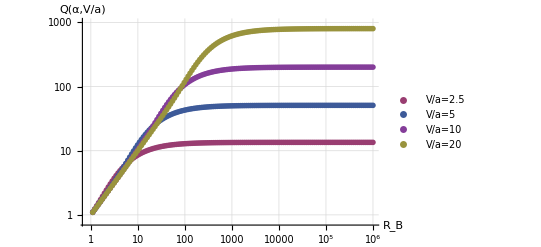

```mathematica
Show[Table[ListLogLogPlot[Legended[Table[{1/alpha,barb[alpha,vOvera]},{alpha,alphaList}],StringForm["V/a=`1`",NumberForm[vOvera,2]]],PlotStyle->ColorData[1][vOvera],PlotRange->{All,1*^3},PlotMarkers-> {Automatic,Medium},PlotLegends->LineLegend[Automatic,LegendMarkerSize->{{50,50}}],GridLines->Automatic,AxesLabel->{"R_B",StringForm["Q(α,V/a)"]},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->16]],{vOvera,{2.5,5,10,20}}]]
```

```mathematica
f=ListInterpolation[Table[{barbAlt[oneOverAlpha,vOvera]},{oneOverAlpha,2,100,1},{vOverA,2.5,5,2.5}]]
```

InterpolatingFunction[…]

```mathematica
Plot3D[f[oneOverAlpha,vOverA],{oneOverAlpha,2,100},{vOverA,2.5,5}]
```

```mathematica
Show[Plot3D[f[oneOverAlpha,vOverA],{oneOverAlpha,2,100},{vOverA,2.5,5}],PlotStyle->ColorData[1][vOvera],PlotRange->{All,1*^2},PlotLegends->LineLegend[Automatic],AxesLabel->{"R_B",StringForm["Q(α,V/a)"]}],{vOvera,{2.5,5,10,20}}]]
```

```mathematica
barb[α_,vOvera_]:=1+(2(1-α)vOvera Exp[-α vOvera^2])/Erfc[-vOvera] NIntegrate[Exp[α x^2]Erfc[x],{x,-vOvera,∞}]
```

```mathematica
barbAlt[oneOver_,vOvera_]:=1+(2(1-oneOver)vOvera Exp[-oneOver vOvera^2])/Erfc[-vOvera] NIntegrate[Exp[oneOver x^2]Erfc[x],{x,-vOvera,∞}]
```

```mathematica
alphaList=PowerRange[0.001,0.99,1.1]
```

```mathematica
Show[Table[ListLogLogPlot[Legended[Table[{1/alpha,barb[alpha,vOvera]},{alpha,alphaList}],StringForm["V/a=`1`",NumberForm[vOvera,2]]],PlotStyle->ColorData[1][vOvera],PlotRange->{All,1*^3},PlotMarkers-> {Automatic,Medium},PlotLegends->LineLegend[Automatic,LegendMarkerSize->{{50,50}}],GridLines->Automatic,AxesLabel->{"R_B",StringForm["Q(α,V/a)"]},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->16]],{vOvera,{2.5,5,10,20}}]]
```